Data Extracted from the Plot

Data:

```mathematica
n=20; (*# data pts*)
(*data's row format: {x,y,total length of error bars,width of bin (in cm, needs to be changed)}*)
data={{23.7500,0.6,0.1846,2},{28.5000,0.6462,0.1538,0.7},{31.1000,0.8077,0.1846,0.5},{32.0000,0.8846,0.2,0.4},{34.2000,0.7538,0.1846,0.4},{36.1000,0.5692,0.1538,0.4},{38.2000,0.6231,0.1538,0.4},{40.0000,0.6538,0.1538,0.4},{41.8000,0.6385,0.1385,0.6},{44.0000,0.5000,0.1231,0.6},{47.0000,0.4231,0.1077,0.8},{50.2000,0.2923,0.0923,0.8},{53.9000,0.4846,0.1385,0.9},{57.7000,0.4231,0.1538,1},{61.7000,0.4692,0.1692,1},{64.8000,0.6154,0.2154,1},{70.0000,0.6769,0.2462,1.2},{76.0000,0.7385,0.3231,1.6},{82.3000,0.6000,0.6154,1.8},{96.2000,0.5385,1.0462,5}}; 
datapts=Table[{Round[data[[i,1]],0.001],Round[data[[i,2]],0.001]},{i,1,n}];
binwidth=Table[Round[data[[i,4]],0.001]*1.8,{i,1,n}];
stdev=Table[Round[data[[i,3]]/2,0.001],{i,1,n}];
Grid[Join[{{"Data from Plot",SpanFromLeft},{"","L_0/E_V_e (km/MeV)","Survival Probability","Error Bar","1/2 Width of the Bin"}},Table[{ToString[i]<>".",datapts[[i,1]],datapts[[i,2]],stdev[[i]],binwidth[[i]]},{i,1,n}]],Frame->All]
```

Data from Plot |  |  |  | 
 | L_0/E_V_e (km/MeV) | Survival Probability | Error Bar | 1/2 Width of the Bin
1. | 23.75 | 0.6 | 0.092 | 3.6
2. | 28.5 | 0.646 | 0.077 | 1.26
3. | 31.1 | 0.808 | 0.092 | 0.9
4. | 32. | 0.885 | 0.1 | 0.72
5. | 34.2 | 0.754 | 0.092 | 0.72
6. | 36.1 | 0.569 | 0.077 | 0.72
7. | 38.2 | 0.623 | 0.077 | 0.72
8. | 40. | 0.654 | 0.077 | 0.72
9. | 41.8 | 0.638 | 0.069 | 1.08
10. | 44. | 0.5 | 0.062 | 1.08
11. | 47. | 0.423 | 0.054 | 1.44
12. | 50.2 | 0.292 | 0.046 | 1.44
13. | 53.9 | 0.485 | 0.069 | 1.62
14. | 57.7 | 0.423 | 0.077 | 1.8
15. | 61.7 | 0.469 | 0.085 | 1.8
16. | 64.8 | 0.615 | 0.108 | 1.8
17. | 70. | 0.677 | 0.123 | 2.16
18. | 76. | 0.738 | 0.162 | 2.88
19. | 82.3 | 0.6 | 0.308 | 3.24
20. | 96.2 | 0.538 | 0.523 | 9.

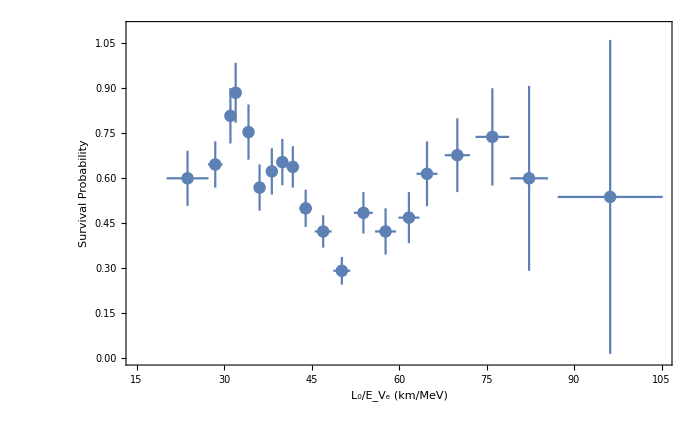

```mathematica
(*Plot Data*)
Needs["ErrorBarPlots`"]
datawitherror=Table[{datapts[[i]],ErrorBar[binwidth[[i]],stdev[[i]]]},{i,1,n}];
dataplot=ErrorListPlot[datawitherror,PlotRange->{{15,105},{0,1.1}}, Frame->True,Axes->False,FrameLabel->{"L_0/E_V_e (km/MeV)", "Survival Probability"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
```

Analysis Using Two Parameters

```mathematica
fitTwo[En_,lambda1_,lambda2_]:=1-lambda1*(Sin[1270*lambda2*L0/En])^2   (* lambda1=Sin^2 2θ lambda2 = Δm^2 *)

L0=180;
y=Table[Integrate[fitTwo[En,lambda1,lambda2],{En,L0/(datapts[[i,1]]+binwidth[[i]]),L0/(datapts[[i,1]]-binwidth[[i]])}],{i,1,n}];
chisquared:=2*Sum[(y[[i]]-datapts[[i,2]])^2/(stdev[[i]])^2,{i,n}];
```

```mathematica
chisq1[lambda1_,lambda2_]:=2*Sum[(y[[i]]-datapts[[i,2]])^2/(stdev[[i]])^2,{i,1,n}]
fit1=FindMinimum[{chisq1[lambda1,lambda2],0.0001≥lambda2≥0,0≤lambda1≤1},{{lambda1,0.8},{lambda2,0.00006}}];
MLE1=lambda1/.fit1[[2]]
MLE2=lambda2/.fit1[[2]]
minCHI=fit1[[1]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

0.582723

0.0000590904

964.864

Minimum χ^2 values for two parameters

```mathematica
chisqtwo95=5.99;
chisqtwo99=9.21;
chisqtwo9973=11.83;
```

Contour Plots

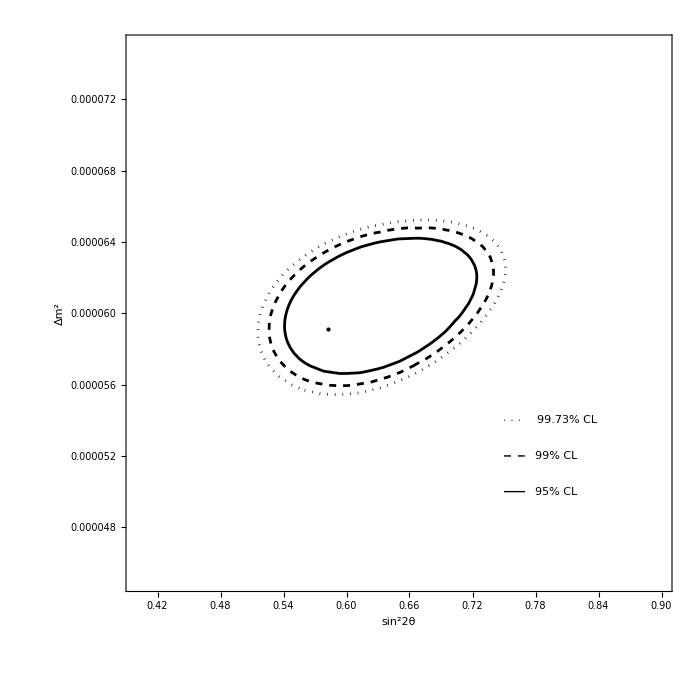

```mathematica
ContourPlot[{chisq1[lambda1,lambda2]-minCHI==chisqtwo95,chisq1[lambda1,lambda2]-minCHI==chisqtwo99,chisq1[lambda1,lambda2]-minCHI==chisqtwo9973},{lambda1,0.4,0.9},{lambda2,0.000045,0.000075},Frame->True,Axes->False,FrameLabel->{"sin^22θ", "Δm^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"},ContourStyle->{{Black,AbsoluteThickness[2]},{Black, AbsoluteThickness[2], Dashed},{Black,Dotted, AbsoluteThickness[2]}},Epilog->{Inset[Text[Style["95% CL"]],{0.8,0.00005}],{Black,Thick,Line[{{0.75,0.00005},{0.77,0.00005}}]},Inset[Text[Style["99% CL"]],{0.8,0.000052}],{Black,Dashed,Thick,Line[{{0.75,0.000052},{0.77,0.000052}}]},Inset[Text[Style["99.73% CL"]],{0.81,0.000054}],{Black,Dotted,Thick,Line[{{0.75,0.000054},{0.77,0.000054}}]},PointSize[Large],Point[{MLE1,MLE2}]}]
```

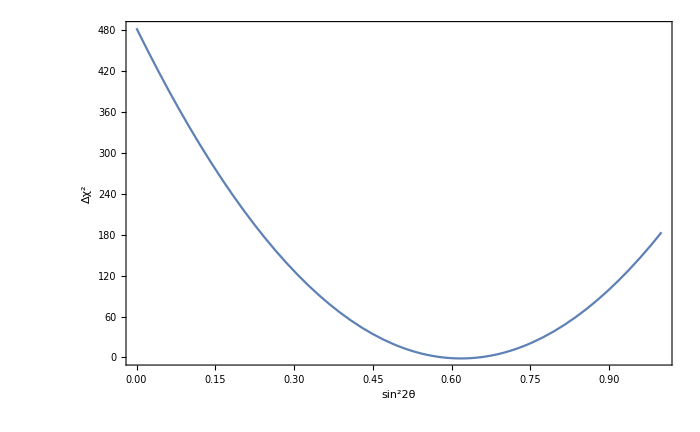

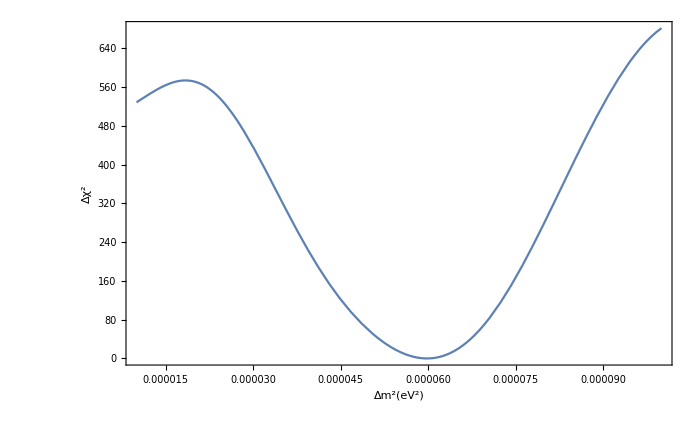

```mathematica
delchisq1mconst[lambda1_]=ReplaceAll[lambda2->0.000059][{chisq1[lambda1,lambda2]}];
delchisq1sinconst[lambda2_]=ReplaceAll[lambda1->0.58][{chisq1[lambda1,lambda2]}];
Plot[{delchisq1mconst[lambda1]-minCHI},{lambda1,0,1},Frame->True,Axes->False,FrameLabel->{"sin^22θ", "Δχ^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
Plot[{delchisq1sinconst[lambda2]-minCHI},{lambda2,0.00001,0.0001},Frame->True,Axes->False,FrameLabel->{"Δm^2(eV^2)", "Δχ^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
```

Analysis Using Three Parameters

```mathematica
fitThree[En_,param1_,param2_,L_]:=1-param1*(Sin[1270*param2*L/En])^2   (* param1=Sin^2 2θ loaram2 = Δm^2 *)

L0=180; L0stdev=20;
ynew=Table[Integrate[fitThree[En,param1,param2,L],{En,L/(datapts[[i,1]]+binwidth[[i]]),L0/(datapts[[i,1]]-binwidth[[i]])}],{i,1,n}];
chisquared2=2*Sum[(ynew[[i]]-datapts[[i,2]])^2/(stdev[[i]])^2,{i,n}];

chisq2[param1_,param2_,L_]:=2*Sum[(ynew[[i]]-datapts[[i,2]])^2/(stdev[[i]])^2,{i,1,n}]+(L0-L)^2/20^2
fit2=FindMinimum[{chisq2[param1,param2,L],0≤param1≤0.9, 0.001≥param2>0},{{param1,0.5},{param2},{L,180}}];
val1=param1/.fit2[[2]]
val2=param2/.fit2[[2]]
val3=L/.fit2[[2]]
minCHIthree=fit2[[1]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

0.481761

0.000162892

163.037

621.526

Minimum χ^2 values for three parameters

```mathematica
chisqthree95=7.81;
chisqthree99=11.34;
chisqthree9973=14.16;
```

Contour Plots

```mathematica
chisq2withL[param1_,param2_]:=ReplaceAll[L->163][{chisq2[param1,param2,L]}]
(*ContourPlot[{chisq2withL[param1,param2]-minCHIthree==chisqthree95,chisq2withL[param1,param2]-minCHIthree==chisqthree99,chisq2withL[param1,param2]-minCHIthree==chisqthree9973},{param1,0.35,1},{param2,0.00012,0.000195},Frame->True,Axes->False,FrameLabel->{"sin^22θ", "Δm^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"},ContourStyle->{{Black,AbsoluteThickness[2]},{Blue, AbsoluteThickness[2]},{Gray, AbsoluteThickness[2]}},Epilog->{Inset[Text[Style["95% CL"]],{0.82,0.000125}],{Black,Thick,Line[{{0.75,0.000125},{0.77,0.000125}}]},Inset[Text[Style["99% CL"]],{0.82,0.000128}],{Blue,Thick,Line[{{0.75,0.000128},{0.77,0.000128}}]},Inset[Text[Style["99.73% CL"]],{0.83,0.000131}],{Gray,Thick,Line[{{0.75,0.000131},{0.77,0.000131}}]}}]*)
```

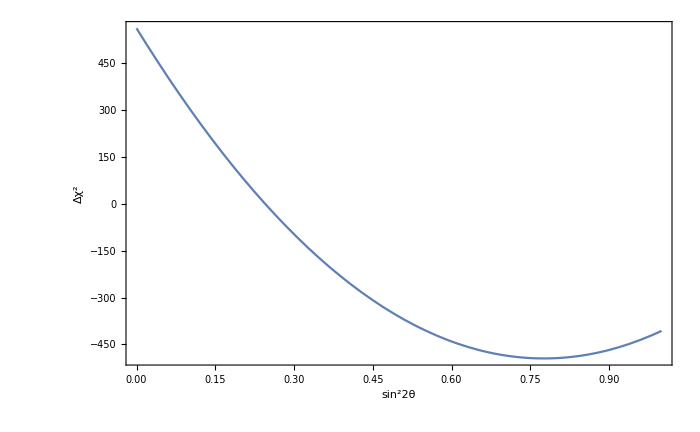

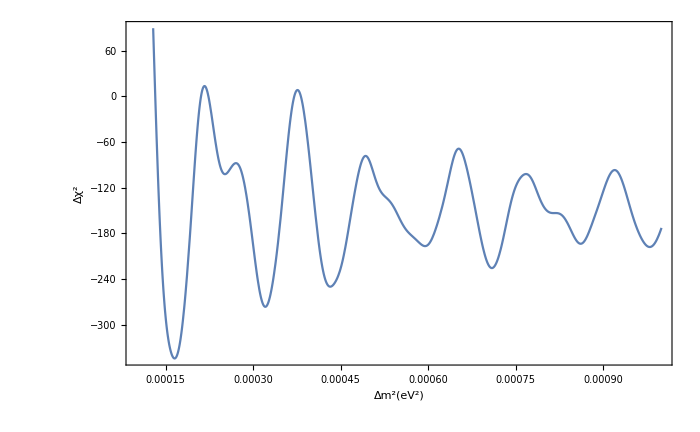

```mathematica
delchisq2mconst[param1_]=ReplaceAll[param2->0.000163][{chisq2withL[param1,param2]}];
delchisq2sinconst[param2_]=ReplaceAll[param1->0.482][{chisq2withL[param1,param2]}];
Plot[{delchisq2mconst[param1]-minCHI},{param1,0,1},Frame->True,Axes->False,FrameLabel->{"sin^22θ", "Δχ^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
Plot[{delchisq2sinconst[param2]-minCHI},{param2,0.0001,0.001},Frame->True,Axes->False,FrameLabel->{"Δm^2(eV^2)", "Δχ^2"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
```